```mathematica
nvec = {{Cos[0],Sin[0]},{Cos[Pi/3],Sin[Pi/3]},{Cos[2 Pi/3],Sin[2 Pi/3]},{Cos[Pi],Sin[Pi]},{Cos[4Pi/3],Sin[4Pi/3]},{Cos[5Pi/3],Sin[5Pi/3]}}
```

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2}}

```mathematica
Kvec[kx_, ky_] := {kx,ky}
```

```mathematica
PhaseFactors[kx_,ky_]=Exp[I nvec.Kvec[kx,ky]]
```

{ⅇ^(ⅈ kx),ⅇ^(ⅈ (kx/2+(√3 ky)/2)),ⅇ^(ⅈ (-kx/2+(√3 ky)/2)),ⅇ^(-ⅈ kx),ⅇ^(ⅈ (-kx/2-(√3 ky)/2)),ⅇ^(ⅈ (kx/2-(√3 ky)/2))}

```mathematica
cosList = ComplexExpand[Re[PhaseFactors[kx,ky]]]
```

{Cos[kx],Cos[kx/2+(√3 ky)/2],Cos[kx/2-(√3 ky)/2],Cos[kx],Cos[kx/2+(√3 ky)/2],Cos[kx/2-(√3 ky)/2]}

```mathematica
e1 = {1,0}
e2 = {-1/2,(√3)/2}

reciprocal = Inverse[Transpose[{e1,e2}]]
```

{1,0}

{-1/2,(√3)/2}

{{1,1/(√3)},{0,2/(√3)}}

```mathematica
Eigenvalue[kx_,ky_]  = 6 -6 Mean[cosList]
```

6-2 Cos[kx]-2 Cos[kx/2-(√3 ky)/2]-2 Cos[kx/2+(√3 ky)/2]

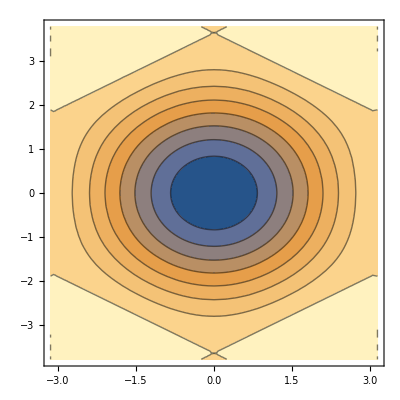

```mathematica
ContourPlot[Eigenvalue[kx,ky] ,{kx,-Pi,Pi} ,{ky,-1.2Pi,1.2Pi}]
```

```mathematica
(* Discrete Periodic kx = 2Pi n1/L and  - kx/2 + Sqrt[3] ky/2 =  2 Pi n2/L 
or  Sqrt[3] ky/2 = (n1 + 2 n2) Pi /L  *)
```

```mathematica
discretEigevalues[n1_,n2_,L_] = Eigenvalue[ 2 Pi n1 /L, (2/Sqrt[3]) (n1 + 2 n2 ) Pi/L]
```

6-2 Cos[(2 n1 π)/L]-2 Cos[(n1 π)/L-((n1+2 n2) π)/L]-2 Cos[(n1 π)/L+((n1+2 n2) π)/L]

```mathematica
EigenvSpect = Table[discretEigevalues[n1,n2,16]//N,{n1,0,15},{n2,0,15}]
```

{{0.,0.304482,1.17157,2.46927,4.,5.53073,6.82843,7.69552,8.,7.69552,6.82843,5.53073,4.,2.46927,1.17157,0.304482},{0.304482,0.890268,1.97266,3.38687,4.91761,6.33182,7.41421,8.,8.,7.41421,6.33182,4.91761,3.38687,1.97266,0.890268,0.304482},{1.17157,1.97266,3.17157,4.58579,6.,7.19891,8.,8.2813,8.,7.19891,6.,4.58579,3.17157,1.97266,1.17157,0.890268},{2.46927,3.38687,4.58579,5.88348,7.08239,8.,8.49661,8.49661,8.,7.08239,5.88348,4.58579,3.38687,2.46927,1.97266,1.97266},{4.,4.91761,6.,7.08239,8.,8.61313,8.82843,8.61313,8.,7.08239,6.,4.91761,4.,3.38687,3.17157,3.38687},{5.53073,6.33182,7.19891,8.,8.61313,8.94495,8.94495,8.61313,8.,7.19891,6.33182,5.53073,4.91761,4.58579,4.58579,4.91761},{6.82843,7.41421,8.,8.49661,8.82843,8.94495,8.82843,8.49661,8.,7.41421,6.82843,6.33182,6.,5.88348,6.,6.33182},{7.69552,8.,8.2813,8.49661,8.61313,8.61313,8.49661,8.2813,8.,7.69552,7.41421,7.19891,7.08239,7.08239,7.19891,7.41421},{8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.},{7.69552,7.41421,7.19891,7.08239,7.08239,7.19891,7.41421,7.69552,8.,8.2813,8.49661,8.61313,8.61313,8.49661,8.2813,8.},{6.82843,6.33182,6.,5.88348,6.,6.33182,6.82843,7.41421,8.,8.49661,8.82843,8.94495,8.82843,8.49661,8.,7.41421},{5.53073,4.91761,4.58579,4.58579,4.91761,5.53073,6.33182,7.19891,8.,8.61313,8.94495,8.94495,8.61313,8.,7.19891,6.33182},{4.,3.38687,3.17157,3.38687,4.,4.91761,6.,7.08239,8.,8.61313,8.82843,8.61313,8.,7.08239,6.,4.91761},{2.46927,1.97266,1.97266,2.46927,3.38687,4.58579,5.88348,7.08239,8.,8.49661,8.49661,8.,7.08239,5.88348,4.58579,3.38687},{1.17157,0.890268,1.17157,1.97266,3.17157,4.58579,6.,7.19891,8.,8.2813,8.,7.19891,6.,4.58579,3.17157,1.97266},{0.304482,0.304482,0.890268,1.97266,3.38687,4.91761,6.33182,7.41421,8.,8.,7.41421,6.33182,4.91761,3.38687,1.97266,0.890268}}

```mathematica
MatrixForm[EigenvSpect]
```

(0. | 0.304482 | 1.17157 | 2.46927 | 4. | 5.53073 | 6.82843 | 7.69552 | 8. | 7.69552 | 6.82843 | 5.53073 | 4. | 2.46927 | 1.17157 | 0.304482
0.304482 | 0.890268 | 1.97266 | 3.38687 | 4.91761 | 6.33182 | 7.41421 | 8. | 8. | 7.41421 | 6.33182 | 4.91761 | 3.38687 | 1.97266 | 0.890268 | 0.304482
1.17157 | 1.97266 | 3.17157 | 4.58579 | 6. | 7.19891 | 8. | 8.2813 | 8. | 7.19891 | 6. | 4.58579 | 3.17157 | 1.97266 | 1.17157 | 0.890268
2.46927 | 3.38687 | 4.58579 | 5.88348 | 7.08239 | 8. | 8.49661 | 8.49661 | 8. | 7.08239 | 5.88348 | 4.58579 | 3.38687 | 2.46927 | 1.97266 | 1.97266
4. | 4.91761 | 6. | 7.08239 | 8. | 8.61313 | 8.82843 | 8.61313 | 8. | 7.08239 | 6. | 4.91761 | 4. | 3.38687 | 3.17157 | 3.38687
5.53073 | 6.33182 | 7.19891 | 8. | 8.61313 | 8.94495 | 8.94495 | 8.61313 | 8. | 7.19891 | 6.33182 | 5.53073 | 4.91761 | 4.58579 | 4.58579 | 4.91761
6.82843 | 7.41421 | 8. | 8.49661 | 8.82843 | 8.94495 | 8.82843 | 8.49661 | 8. | 7.41421 | 6.82843 | 6.33182 | 6. | 5.88348 | 6. | 6.33182
7.69552 | 8. | 8.2813 | 8.49661 | 8.61313 | 8.61313 | 8.49661 | 8.2813 | 8. | 7.69552 | 7.41421 | 7.19891 | 7.08239 | 7.08239 | 7.19891 | 7.41421
8. | 8. | 8. | 8. | 8. | 8. | 8. | 8. | 8. | 8. | 8. | 8. | 8. | 8. | 8. | 8.
7.69552 | 7.41421 | 7.19891 | 7.08239 | 7.08239 | 7.19891 | 7.41421 | 7.69552 | 8. | 8.2813 | 8.49661 | 8.61313 | 8.61313 | 8.49661 | 8.2813 | 8.
6.82843 | 6.33182 | 6. | 5.88348 | 6. | 6.33182 | 6.82843 | 7.41421 | 8. | 8.49661 | 8.82843 | 8.94495 | 8.82843 | 8.49661 | 8. | 7.41421
5.53073 | 4.91761 | 4.58579 | 4.58579 | 4.91761 | 5.53073 | 6.33182 | 7.19891 | 8. | 8.61313 | 8.94495 | 8.94495 | 8.61313 | 8. | 7.19891 | 6.33182
4. | 3.38687 | 3.17157 | 3.38687 | 4. | 4.91761 | 6. | 7.08239 | 8. | 8.61313 | 8.82843 | 8.61313 | 8. | 7.08239 | 6. | 4.91761
2.46927 | 1.97266 | 1.97266 | 2.46927 | 3.38687 | 4.58579 | 5.88348 | 7.08239 | 8. | 8.49661 | 8.49661 | 8. | 7.08239 | 5.88348 | 4.58579 | 3.38687
1.17157 | 0.890268 | 1.17157 | 1.97266 | 3.17157 | 4.58579 | 6. | 7.19891 | 8. | 8.2813 | 8. | 7.19891 | 6. | 4.58579 | 3.17157 | 1.97266
0.304482 | 0.304482 | 0.890268 | 1.97266 | 3.38687 | 4.91761 | 6.33182 | 7.41421 | 8. | 8. | 7.41421 | 6.33182 | 4.91761 | 3.38687 | 1.97266 | 0.890268)

```mathematica
Flatten[EigenvSpect]
```

{0.,0.304482,1.17157,2.46927,4.,5.53073,6.82843,7.69552,8.,7.69552,6.82843,5.53073,4.,2.46927,1.17157,0.304482,0.304482,0.890268,1.97266,3.38687,4.91761,6.33182,7.41421,8.,8.,7.41421,6.33182,4.91761,3.38687,1.97266,0.890268,0.304482,1.17157,1.97266,3.17157,4.58579,6.,7.19891,8.,8.2813,8.,7.19891,6.,4.58579,3.17157,1.97266,1.17157,0.890268,2.46927,3.38687,4.58579,5.88348,7.08239,8.,8.49661,8.49661,8.,7.08239,5.88348,4.58579,3.38687,2.46927,1.97266,1.97266,4.,4.91761,6.,7.08239,8.,8.61313,8.82843,8.61313,8.,7.08239,6.,4.91761,4.,3.38687,3.17157,3.38687,5.53073,6.33182,7.19891,8.,8.61313,8.94495,8.94495,8.61313,8.,7.19891,6.33182,5.53073,4.91761,4.58579,4.58579,4.91761,6.82843,7.41421,8.,8.49661,8.82843,8.94495,8.82843,8.49661,8.,7.41421,6.82843,6.33182,6.,5.88348,6.,6.33182,7.69552,8.,8.2813,8.49661,8.61313,8.61313,8.49661,8.2813,8.,7.69552,7.41421,7.19891,7.08239,7.08239,7.19891,7.41421,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,7.69552,7.41421,7.19891,7.08239,7.08239,7.19891,7.41421,7.69552,8.,8.2813,8.49661,8.61313,8.61313,8.49661,8.2813,8.,6.82843,6.33182,6.,5.88348,6.,6.33182,6.82843,7.41421,8.,8.49661,8.82843,8.94495,8.82843,8.49661,8.,7.41421,5.53073,4.91761,4.58579,4.58579,4.91761,5.53073,6.33182,7.19891,8.,8.61313,8.94495,8.94495,8.61313,8.,7.19891,6.33182,4.,3.38687,3.17157,3.38687,4.,4.91761,6.,7.08239,8.,8.61313,8.82843,8.61313,8.,7.08239,6.,4.91761,2.46927,1.97266,1.97266,2.46927,3.38687,4.58579,5.88348,7.08239,8.,8.49661,8.49661,8.,7.08239,5.88348,4.58579,3.38687,1.17157,0.890268,1.17157,1.97266,3.17157,4.58579,6.,7.19891,8.,8.2813,8.,7.19891,6.,4.58579,3.17157,1.97266,0.304482,0.304482,0.890268,1.97266,3.38687,4.91761,6.33182,7.41421,8.,8.,7.41421,6.33182,4.91761,3.38687,1.97266,0.890268}

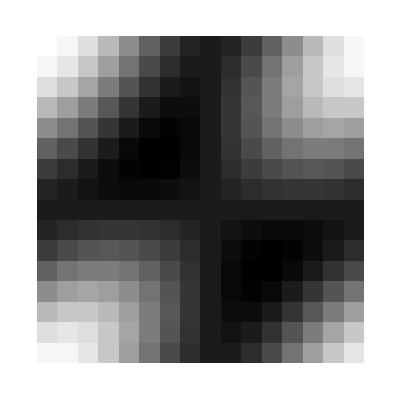

```mathematica
ArrayPlot[%171]
```

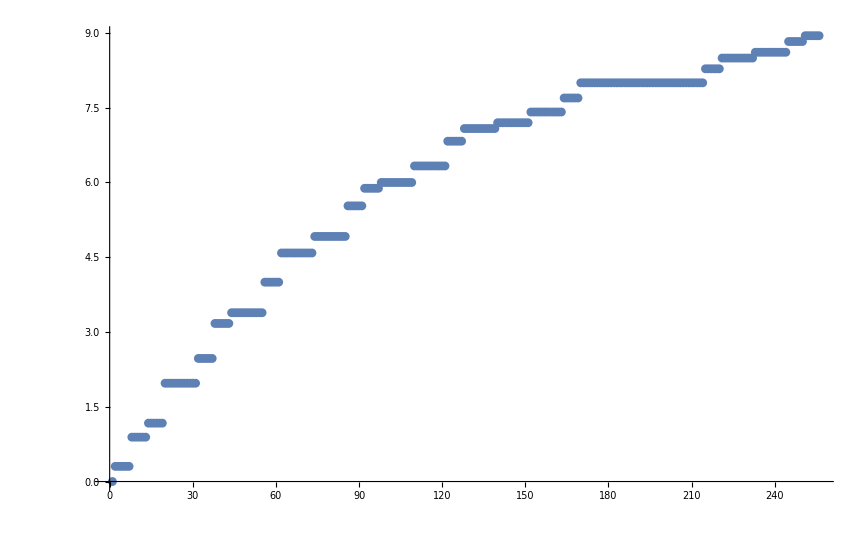

```mathematica
ListPlot[Sort[Flatten[EigenvSpect]]]
```

```mathematica
ListEivenvalues[n1_,n2_,L_] := Sort[Flatten[Table[discretEigevalues[n1,n2,L]//N,{n1,0,L-1},{n2,0,L-1}]]]
```

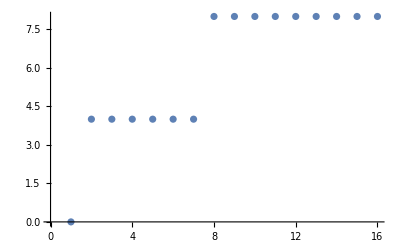

```mathematica
ListPlot[ListEivenvalues[n1,n2,4]]
```

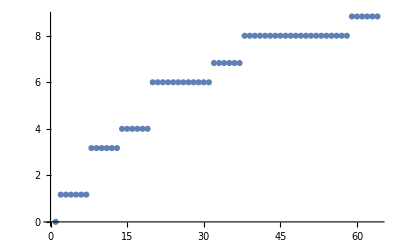

```mathematica
ListPlot[ListEivenvalues[n1,n2,8]]
```